```mathematica
m=1.;α=0.2;n=16;tf=100.;p=2;
```

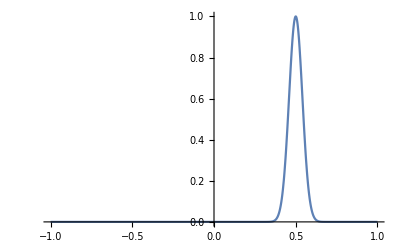

```mathematica
Plot[Exp[-300*(x-0.5)^2],{x,-1,1},PlotRange->All]
```

```mathematica
nsol=NDSolveValue[Flatten[{Table[m x[i]''[t]==(x[i + 1][t] - 2*x[i][t] + x[i - 1][t])(1+ α*(x[i + 1][t] - x[i-1][t])),{i,n}]/.{x[0][t]:>x[1][t]-1,x[n+1][t]:>x[n][t]+1},Table[{x[i][0]==i,x[i]'[0]==RandomReal[{-1,1}]},{i,n}]}],Table[x[i],{i,n}],{t,0,tf}];
```

-Graphics-

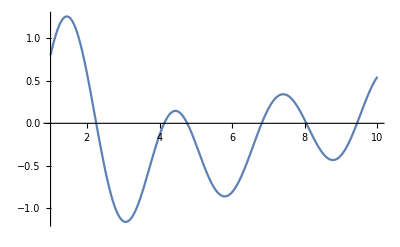

```mathematica
Plot[Table[nsol[i][t], {i, 1,n}], {t, 0, tf}, 
       PlotRange -> All,  Frame -> True, Axes -> False, 
       ImageSize -> 450, AspectRatio -> 1]
```

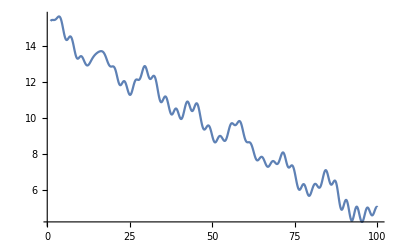
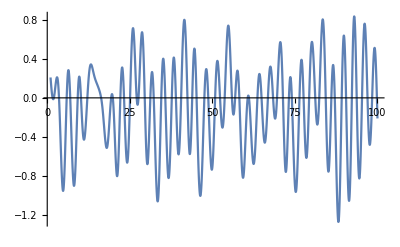

```mathematica
j=15;
{Plot[nsol[[j]][t],{t,1,tf}],Plot[D[nsol[[j]][τ],τ]/.τ->t,{t,1,tf}]}
```